## solve for prescribed path for ODE (Problem 4.2)

```mathematica
Clear["Global`*"]
```

```mathematica
xprescribed=Piecewise[{{2(t/τ)^2,0<t<τ/2},{1-2(1-t/τ)^2,t≥τ/2}}];
xprescribed=2 (t/τ)^2-(1-2 t/τ)^2 UnitStep[2 t/τ-1];
u=xprescribed + D[xprescribed, t,t]//Simplify
```

Piecewise[{{Indeterminate, (2 t)/τ==1}, {-(4+2 t^2-4 t τ+τ^2)/τ^2, (2 t)/τ≥1}, {(2 (2+t^2))/τ^2, True}}]

```mathematica
{xprescribed,D[xprescribed, t],D[xprescribed, t,t]}//Simplify
```

{(2 t^2-(-2 t+τ)^2 UnitStep[-1+(2 t)/τ])/τ^2,Piecewise[{{Indeterminate, (2 t)/τ==1}, {(4 (-t+τ))/τ^2, (2 t)/τ≥1}, {(4 t)/τ^2, True}}],Piecewise[{{Indeterminate, (2 t)/τ==1}, {-4/τ^2, (2 t)/τ≥1}, {4/τ^2, True}}]}

```mathematica
{xprescribed,D[xprescribed, t]}/.{τ->1,t->0}
```

{0,0}

```mathematica
xsol=DSolveValue[{x''[t]+x[t]==u,x[0]==x'[0]==0},x[t],t,Assumptions->{τ>t>0}]//Simplify
```

Piecewise[{{Indeterminate, (2 t)/τ==1}, {-1-(2 t^2)/τ^2+(4 t)/τ, (2 t)/τ≥1}, {(2 t^2)/τ^2, True}}]

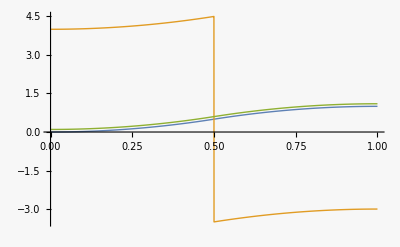

```mathematica
Plot[{xprescribed/.τ->1,u/.τ->1,xsol+0.1/.τ->1},{t,0,1},PlotRange->All]
```

```mathematica
(* Adding 0.1 shows that both ways of computing the trajectory give the same result! *)
```